## Pulse Width Modulation Principle

```mathematica
Manipulate[
Plot[{((Sin[x]*m)+(Sin[x*3]*1/3*d)),If[x<π,1,-1]*If[s,1,0]*(2.5*Abs[Round[(c/2*x)/π]-(c/2*x)/π]),If[x<π,If[((Sin[x]*m)+(Sin[x*3]*1/3*d))≥(2.5*Abs[Round[(c/2*x)/π]-(c/2*x)/π]),1.25,0],If[((Sin[x]*m)+(Sin[x*3]*1/3*d))≤(-2.5*Abs[Round[(c/2*x)/π]-(c/2*x)/π]),-1.25,0]]},{x,0,2π},
PlotStyle->{{RGBColor[0.7,0.9,0.3],Thickness[0.005]},
{RGBColor[0.1,0.33,1],Thickness[0.002]},
{RGBColor[1,0.33,0.1],Thickness[0.002]}},
AxesLabel->{"time",
"voltage"
},
PlotPoints->500,
AxesOrigin->{0,0},
PlotRange->{-1.4,1.4},
PlotLabel->Style["pulse width modulation",14],
Filling->{1->Axis,3->Axis},
FillingStyle->Automatic,
PerformanceGoal->"Quality",
ImageSize->{550, 390}
],
{{c,24,"relative carrier frequency" },{12,24,48},
ControlType->SetterBar},
{{s,True,"show carrier triangle signal"},{True,False}},
{{m,1,"reference magnitude (-60% +20%)"},
0.4,1.2,Appearance->"Labeled"},
{{d,0,"reference distortion"},
0,1,Appearance->"Labeled"},
TrackedSymbols:>Manipulate
]
```

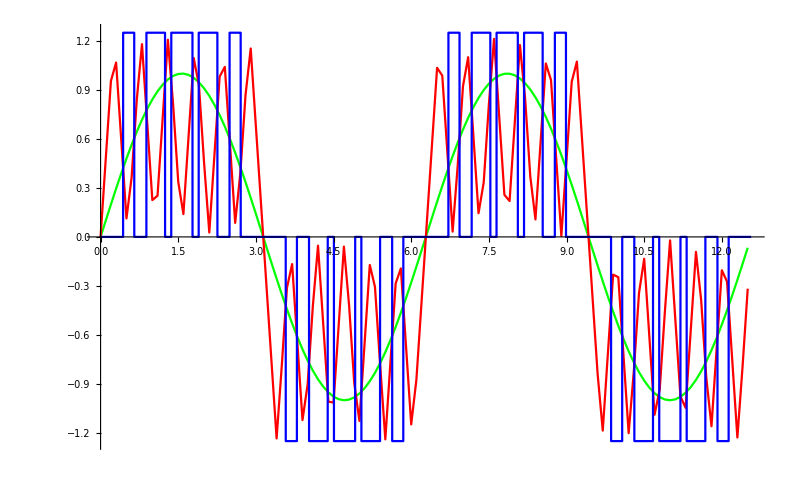

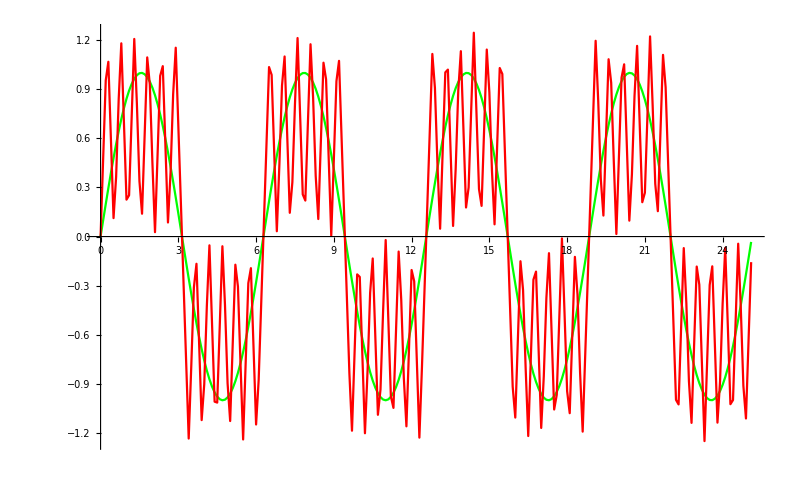

Show::gcomb: Could not combine the graphics objects in Show[{aaaa1,}].

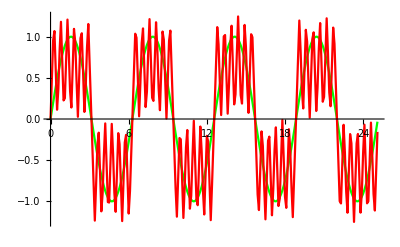
Show[{aaaa1,-Graphics-}]

```mathematica
ClearAll;
DD=0.1;
NN=12;
SS1[x_]:=N[Sin[x],15];
SS2[x_]:=If[Sin[x]<0,-1,1];
TT1[x_,n_]:=N[2.5*Abs[Round[(n/2*x)/π]-((n/2*x)/π)],15];
TT3[x_,n_]:=TT1[x,n]*SS2[x]
TT4[x_,n_]:=If[Abs[SS1[x]]>TT2[x,n],1.25*SS2[x],0]
LS1[xx_,yy_,nn_]:=Table[{x,SS1[x]},{x,xx,yy,DD}];
LT3[xx_,yy_,nn_]:=Table[{x,TT3[x,nn]},{x,xx,yy,DD}];
LT4[xx_,yy_,nn_]:=Table[{x,TT4[x,nn]},{x,xx,yy,DD*0.01}];
aaaa2=ListPlot[
{
LS1[0,8π,NN],
LT3[0,8π,NN]
},PlotLegends->"Expressions",Joined->True,PlotStyle->{Green,Red}];
aaaa3=ListPlot[
{
LS1[0,4π,NN],
LT3[0,4π,NN],
LT4[0,4π,NN]
},PlotLegends->"Expressions",Joined->True,PlotStyle->{Green,Red,Blue}];
Show[{aaaa3}]
Show[{aaaa2}]
Show[{aaaa1,aaaa2}]
```